```mathematica
SetDirectory["/Users/beerli/help/zanotto"]
```

/Users/beerli/help/zanotto

```mathematica
getmathfile[filename_]:=Module[{rawdata,replicates,locus,numpop, locations,locations2, headers,numlens},
 rawdata=ReadList[filename,Word];
locations =ToExpression[Flatten[Position[rawdata,"@"]]];
locations2 = Append[locations,Length[rawdata]];

Print[locations2];

numlens = Table[locations2[[i+1]]-locations2[[i]]-1,{i,1,Length[locations2]-1}];
Print[numlens];

replicates = Length[locations];
 rawdata=Flatten[ReadList[filename,Table[Flatten[{Word,Table[Number,{numlens[[i]]}]}],{i,Length[locations]}]]];
Print[rawdata];

headers=Table[rawdata[[Range[locations[[i]]+1,locations[[i]]+5]]],{i,1,replicates}];
Print[headers];

ToExpression[Table[{
Partition[rawdata[[Range[locations[[i]]+6,locations[[i]]+6 +( ToExpression[rawdata[[locations[[i]]+3]] ]ToExpression[rawdata[[locations[[i]]+4]] ]) ]]],ToExpression[rawdata[[locations[[i]]+3]]]]
,
Partition[rawdata[[Range[locations[[i]]+6 +( ToExpression[rawdata[[locations[[i]]+3]] ]ToExpression[rawdata[[locations[[i]]+4]] ]),locations[[i]]+6 +( ToExpression[rawdata[[locations[[i]]+3]] ]ToExpression[rawdata[[locations[[i]]+4]] ])+( ToExpression[rawdata[[locations[[i]]+3]] ]ToExpression[rawdata[[locations[[i]]+4]] ]) ]]],ToExpression[rawdata[[locations[[i]]+3]]]]
},{i,Length[locations]}]
]]
```

```mathematica
nd=getmathfile["polmathfile_lnL"];
```

{1,5191,10380}

{5189,5188}

{@,1,1,36,36,2,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-736.644,-718.255,-700.39,-683.253,-667.129,-652.412,-639.649,-629.603,-623.331,-622.301,-628.555,-644.929,-675.361,-725.324,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-742.112,-722.909,-703.243,-683.603,-664.002,-644.453,-624.977,-605.602,-586.369,-567.331,-548.565,-530.178,-512.316,-495.184,-479.066,-464.358,-451.608,-441.579,-435.33,-434.332,-440.63,-457.061,-487.566,-537.616,-614.805,-729.678,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-729.578,-709.848,-690.122,-670.399,-650.681,-630.971,-611.271,-591.584,-571.918,-552.279,-532.677,-513.128,-493.653,-474.279,-455.046,-436.009,-417.244,-398.858,-380.998,-363.869,-347.755,-333.052,-320.31,-310.291,-304.057,-303.08,-309.408,-325.883,-356.389,-405.878,-483.894,-598.903,-718.3,-698.565,-678.831,-659.098,-639.367,-619.638,-599.911,-580.188,-560.47,-540.76,-521.06,-501.374,-481.707,-462.068,-442.467,-422.918,-403.442,-384.068,-364.835,-345.799,-327.035,-308.649,-290.79,-273.662,-257.55,-242.849,-230.11,-220.095,-213.864,-212.694,-203.145,-205.407,-226.493,-273.763,-357.456,-491.806,-657.749,-638.014,-618.28,-598.548,-578.816,-559.087,-539.36,-519.637,-499.919,-480.209,-460.509,-440.823,-421.156,-401.517,-381.916,-362.367,-342.892,-323.518,-304.285,-285.249,-266.485,-248.101,-230.242,-213.114,-197.002,-182.299,-169.546,-159.475,-147.148,-126.073,-114.725,-116.911,-137.928,-185.142,-268.796,-403.12,-618.479,-598.745,-579.011,-559.278,-539.547,-519.817,-500.091,-480.368,-460.65,-440.94,-421.24,-401.554,-381.888,-362.249,-342.648,-323.099,-303.624,-284.251,-265.019,-245.984,-227.222,-208.838,-190.98,-173.204,-149.777,-127.618,-108.312,-92.9938,-83.2214,-69.4338,-58.0195,-60.1462,-81.1012,-128.281,-211.958,-346.291,-594.357,-574.622,-554.888,-535.156,-515.424,-495.695,-475.968,-456.245,-436.528,-416.818,-397.118,-377.432,-357.766,-338.128,-318.527,-298.98,-279.506,-260.134,-240.905,-221.872,-203.103,-180.907,-154.663,-129.229,-105.103,-82.9463,-63.6209,-48.2714,-38.4565,-35.1043,-23.9784,-25.9297,-46.5935,-93.6822,-177.751,-312.378,-581.103,-561.368,-541.634,-521.901,-502.17,-482.441,-462.714,-442.991,-423.274,-403.564,-383.864,-364.179,-344.513,-324.875,-305.275,-285.729,-266.256,-246.886,-227.658,-208.306,-182.366,-155.627,-129.514,-104.238,-80.204,-58.0678,-38.7219,-23.3343,-13.4572,-11.1297,-5.97551,-7.51576,-27.799,-74.8141,-159.33,-294.872,-575.811,-556.077,-536.343,-516.61,-496.879,-477.15,-457.423,-437.7,-417.983,-398.273,-378.573,-358.888,-339.222,-319.585,-299.985,-280.439,-260.967,-241.598,-222.342,-198.279,-171.084,-144.408,-118.422,-93.3302,-69.4508,-47.377,-28.0246,-12.5885,-2.51005,0.698999,0.474024,-0.84922,-21.0115,-68.0292,-152.687,-289.049,-576.355,-556.62,-536.886,-517.153,-497.422,-477.693,-457.966,-438.244,-418.526,-398.816,-379.117,-359.431,-339.766,-320.128,-300.529,-280.983,-261.511,-242.143,-222.767,-197.149,-169.961,-143.316,-117.406,-92.4622,-68.7745,-46.8323,-27.5133,-11.9949,-1.24954,3.12545,-0.846582,-2.9867,-23.1373,-70.1839,-154.897,-291.678,-581.135,-561.401,-541.667,-521.934,-502.203,-482.473,-462.747,-443.024,-423.307,-403.597,-383.897,-364.212,-344.547,-324.909,-305.31,-285.764,-266.293,-246.924,-227.66,-203.333,-176.154,-149.523,-123.648,-98.7926,-75.2724,-53.5179,-34.2928,-18.623,-7.0496,-2.24634,-7.45625,-11.5512,-31.725,-78.8091,-163.559,-300.527,-588.975,-569.241,-549.507,-529.774,-510.043,-490.313,-470.587,-450.864,-431.147,-411.437,-391.737,-372.052,-352.387,-332.749,-313.15,-293.604,-274.133,-254.765,-235.538,-214.633,-187.616,-160.99,-135.131,-110.318,-86.9069,-65.3355,-46.2487,-30.4194,-18.4146,-13.5057,-18.9854,-24.7619,-44.9741,-92.0989,-176.881,-313.934,-599.017,-579.282,-559.548,-539.816,-520.084,-500.355,-480.628,-460.906,-441.188,-421.478,-401.779,-382.094,-362.428,-342.791,-323.192,-303.646,-284.175,-264.806,-245.581,-226.525,-202.865,-176.248,-150.394,-125.601,-102.247,-80.8018,-61.8337,-45.9359,-33.9253,-29.0361,-34.3805,-41.3188,-61.5795,-108.748,-193.559,-330.651,-610.638,-590.903,-571.169,-551.437,-531.705,-511.976,-492.249,-472.527,-452.809,-433.099,-413.4,-393.715,-374.049,-354.412,-334.813,-315.267,-295.796,-276.428,-257.203,-238.176,-219.211,-194.234,-168.384,-143.599,-120.272,-98.8887,-79.9597,-64.0309,-52.3018,-47.0309,-50.553,-58.3681,-80.5932,-127.812,-212.652,-349.758,-623.388,-603.654,-583.92,-564.187,-544.456,-524.727,-505,-485.277,-465.56,-445.85,-426.15,-406.465,-386.8,-367.162,-347.563,-328.018,-308.546,-289.178,-269.953,-250.927,-232.176,-213.284,-188.337,-163.556,-140.239,-118.871,-99.6988,-82.0298,-67.5322,-59.3219,-60.3906,-66.3598,-93.86,-147.259,-233.413,-370.46,-636.943,-617.209,-597.475,-577.742,-558.011,-538.281,-518.555,-498.832,-479.115,-459.405,-439.705,-420.02,-400.355,-380.717,-361.118,-341.572,-322.101,-302.733,-283.508,-264.482,-245.731,-227.359,-208.885,-184.923,-161.493,-137.901,-115.076,-95.8257,-80.7571,-72.4221,-70.4062,-76.2001,-103.678,-157.519,-246.169,-373.27,-651.067,-631.332,-611.599,-591.866,-572.135,-552.405,-532.679,-512.956,-493.239,-473.529,-453.829,-434.144,-414.479,-394.841,-375.242,-355.696,-336.225,-316.857,-297.632,-278.606,-259.855,-241.484,-223.585,-205.14,-178.403,-152.732,-129.831,-110.469,-95.0472,-86.6795,-81.7093,-87.4749,-114.914,-168.702,-257.449,-374.561,-665.591,-645.856,-626.123,-606.39,-586.658,-566.929,-547.203,-527.48,-507.762,-488.053,-468.353,-448.668,-429.002,-409.365,-389.765,-370.22,-350.748,-331.38,-312.155,-293.129,-274.379,-256.008,-238.11,-220.087,-193.886,-168.214,-145.324,-125.795,-110.11,-101.656,-94.0209,-99.7678,-127.147,-180.755,-269.618,-376.32,-680.393,-660.659,-640.925,-621.192,-601.461,-581.731,-562.005,-542.282,-522.565,-502.855,-483.155,-463.47,-443.805,-424.167,-404.568,-385.022,-365.55,-346.182,-326.957,-307.931,-289.181,-270.81,-252.917,-235.083,-209.891,-184.215,-161.32,-141.581,-125.721,-116.409,-107.043,-112.775,-140.063,-193.425,-282.223,-378.416,-695.387,-675.653,-655.919,-636.186,-616.455,-596.726,-576.999,-557.276,-537.559,-517.849,-498.149,-478.464,-458.799,-439.161,-419.562,-400.016,-380.544,-361.176,-341.95,-322.924,-304.174,-285.804,-267.917,-250.191,-226.253,-200.57,-177.654,-157.682,-141.714,-130.3,-120.546,-126.095,-152.255,-202.824,-286.304,-380.755,-710.512,-690.777,-671.044,-651.311,-631.579,-611.85,-592.124,-572.401,-552.683,-532.973,-513.274,-493.588,-473.923,-454.285,-434.686,-415.14,-395.668,-376.299,-357.074,-338.047,-319.297,-300.927,-283.048,-265.401,-242.848,-217.164,-194.21,-174.002,-157.967,-141.181,-127.029,-129.302,-154.241,-205.702,-288.854,-383.267,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-741.013,-730.486,-723.955,-723.017,-729.858,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-741.013,-720.677,-700.321,-680.108,-660.093,-640.354,-620.996,-602.172,-584.092,-567.057,-551.491,-537.991,-527.391,-520.845,-519.938,-526.852,-544.587,-577.316,-630.889,-713.475,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-739.714,-719.03,-698.343,-677.671,-657.018,-636.392,-615.804,-595.268,-574.804,-554.438,-534.208,-514.166,-494.382,-474.957,-456.04,-437.844,-420.682,-404.995,-391.398,-380.74,-374.186,-373.339,-380.391,-398.329,-431.238,-484.889,-567.489,-690.351,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-738.328,-717.599,-696.883,-676.169,-655.46,-634.755,-614.058,-593.37,-572.697,-552.042,-531.414,-510.822,-490.278,-469.801,-449.414,-429.149,-409.05,-389.183,-369.65,-350.606,-332.284,-315.012,-299.241,-285.588,-274.901,-268.346,-267.533,-274.679,-292.805,-325.971,-379.778,-438.483,-534.819,-681.357,-704.211,-683.49,-662.771,-642.052,-621.336,-600.622,-579.912,-559.207,-538.509,-517.821,-497.145,-476.488,-455.855,-435.256,-414.699,-394.201,-373.779,-353.459,-333.283,-313.32,-293.682,-274.542,-256.142,-238.814,-223.005,-209.328,-198.626,-192.058,-191.218,-198.318,-216.479,-248.702,-271.297,-324.368,-419.761,-545.55,-649.841,-629.12,-608.401,-587.682,-566.965,-546.251,-525.541,-504.835,-484.135,-463.445,-442.767,-422.106,-401.466,-380.855,-360.28,-339.752,-319.286,-298.906,-278.656,-258.615,-238.907,-219.712,-201.273,-183.918,-168.089,-154.386,-143.606,-136.759,-135.285,-141.682,-159.526,-167.002,-188.946,-241.359,-324.522,-446.72,-610.712,-589.991,-569.271,-548.552,-527.835,-507.12,-486.408,-465.701,-445,-424.307,-403.625,-382.957,-362.308,-341.682,-321.085,-300.525,-280.015,-259.581,-239.274,-219.181,-199.433,-180.209,-161.749,-144.374,-128.504,-114.657,-103.381,-95.6535,-93.5154,-99.6452,-105.357,-107.551,-129.039,-176.202,-252.915,-375.004,-582.55,-561.829,-541.109,-520.389,-499.672,-478.956,-458.243,-437.534,-416.83,-396.133,-375.446,-354.77,-334.108,-313.465,-292.844,-272.252,-251.703,-231.227,-210.881,-190.758,-170.987,-151.748,-133.269,-115.845,-99.7854,-85.3785,-73.3721,-65.3084,-63.1074,-62.9927,-56.7997,-60.9766,-80.8593,-124.671,-201.293,-322.812,-562.283,-541.561,-520.84,-500.12,-479.401,-458.684,-437.97,-417.258,-396.551,-375.849,-355.154,-334.468,-313.793,-293.131,-272.486,-251.864,-231.284,-210.778,-190.408,-170.267,-150.485,-131.229,-112.692,-94.9794,-78.1306,-62.9494,-50.7589,-42.8738,-40.8878,-27.2527,-20.2166,-22.9715,-43.1551,-87.3415,-164.1,-284.3,-547.696,-526.974,-506.252,-485.531,-464.812,-444.093,-423.376,-402.661,-381.949,-361.241,-340.538,-319.841,-299.151,-278.471,-257.803,-237.157,-216.552,-196.026,-175.642,-155.492,-135.7,-116.396,-97.573,-79.0362,-61.4835,-46.0924,-33.9094,-26.1432,-19.401,-0.898182,8.00339,5.93732,-14.8932,-60.0182,-137.28,-255.187,-537.197,-516.475,-495.753,-475.031,-454.31,-433.589,-412.87,-392.152,-371.435,-350.721,-330.009,-309.301,-288.597,-267.899,-247.212,-226.546,-205.924,-185.385,-164.992,-144.836,-125.023,-105.564,-86.1297,-66.9897,-49.2572,-33.8259,-21.6316,-13.8644,-0.372888,18.5272,29.1702,27.1619,6.0279,-39.9222,-117.891,-233.213,-529.641,-508.919,-488.196,-467.473,-446.75,-426.028,-405.306,-384.585,-363.864,-343.143,-322.424,-301.705,-280.989,-260.277,-239.574,-218.893,-198.258,-177.71,-157.313,-137.151,-117.29,-97.5316,-77.5518,-58.1979,-40.42,-24.971,-12.7573,-4.95465,13.4333,33.0897,44.5226,42.5123,21.2522,-25.2436,-103.833,-217.222,-524.203,-503.48,-482.756,-462.033,-441.309,-420.585,-399.861,-379.136,-358.411,-337.686,-316.959,-296.232,-275.505,-254.781,-234.066,-213.374,-192.731,-172.177,-151.777,-131.606,-111.666,-91.5615,-71.2733,-51.8468,-34.0515,-18.5902,-6.35728,1.52244,23.5097,43.9065,55.5939,53.5801,32.2609,-14.589,-93.6285,-205.687,-520.289,-499.566,-478.842,-458.117,-437.392,-416.667,-395.941,-375.214,-354.485,-333.755,-313.023,-292.289,-271.554,-250.821,-230.097,-209.397,-188.747,-168.19,-147.787,-127.604,-107.566,-87.168,-66.7262,-47.27,-29.4653,-13.9946,-1.7453,6.52734,30.9064,51.7966,63.5685,61.5525,40.2023,-6.8802,-86.2285,-197.38,-517.472,-496.748,-476.024,-455.299,-434.573,-413.847,-393.119,-372.39,-351.659,-330.925,-310.188,-289.449,-268.707,-247.967,-227.237,-206.531,-185.877,-165.317,-144.912,-124.716,-104.577,-83.9652,-63.4449,-43.9742,-26.1635,-10.6856,1.57688,10.8392,36.3316,57.505,69.3103,67.293,45.9251,-1.31243,-80.8723,-191.4,-515.445,-494.721,-473.996,-453.27,-432.544,-411.817,-391.088,-370.357,-349.624,-328.887,-308.147,-287.403,-266.657,-245.912,-225.176,-204.466,-183.809,-163.248,-142.841,-122.632,-102.401,-81.6436,-61.0804,-41.6015,-23.7867,-8.30335,3.96939,14.3301,40.2911,61.6229,73.4437,71.4257,50.0469,2.70455,-77.002,-187.095,-513.986,-493.261,-472.536,-451.81,-431.084,-410.356,-389.626,-368.894,-348.159,-327.42,-306.677,-285.93,-265.18,-244.432,-223.693,-202.98,-182.321,-161.758,-141.35,-121.129,-100.823,-79.9659,-59.3774,-39.8936,-22.0758,-6.58843,5.69208,16.9409,43.1671,64.59,76.419,74.4004,53.0147,5.60056,-74.2088,-183.996,-512.936,-492.211,-471.486,-450.76,-430.033,-409.304,-388.573,-367.84,-347.104,-326.364,-305.619,-284.87,-264.117,-243.366,-222.624,-201.909,-181.249,-160.686,-140.276,-120.045,-99.6791,-78.7554,-58.1513,-38.6643,-20.8445,-5.35401,6.93232,18.8447,45.2491,66.7267,78.5605,76.5416,55.1513,7.68735,-72.1947,-181.766,-512.18,-491.455,-470.73,-450.004,-429.276,-408.547,-387.816,-367.082,-346.345,-325.604,-304.857,-284.106,-263.352,-242.599,-221.855,-201.139,-180.477,-159.913,-139.503,-119.263,-98.8524,-77.8828,-57.2687,-37.7795,-19.9582,-4.46548,7.82514,20.2227,46.7532,68.2651,80.1018,78.0827,56.6893,9.19051,-70.7433,-180.161,-511.636,-490.911,-470.186,-449.459,-428.732,-408.002,-387.271,-366.537,-345.799,-325.056,-304.309,-283.557,-262.801,-242.046,-221.302,-200.584,-179.922,-159.357,-138.946,-118.7,-98.2555,-77.2542,-56.6334,-37.1427,-19.3203,-3.82596,8.46781,21.2177,47.8384,69.3726,81.2111,79.1918,57.7964,10.273,-69.6978,-179.005,-511.245,-490.52,-469.794,-449.068,-428.34,-407.61,-386.878,-366.144,-345.405,-324.663,-303.915,-283.161,-262.405,-241.649,-220.903,-200.185,-179.522,-158.957,-138.546,-118.295,-97.825,-76.8015,-56.1761,-36.6844,-18.8612,-3.36567,8.93039,21.9352,48.6208,70.1697,82.0095,79.9901,58.5932,11.0524,-68.9449,-178.174,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-735.477,-723.488,-722.076,-735.357,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-717.324,-680.897,-645.528,-611.629,-579.773,-550.756,-525.683,-506.091,-494.112,-492.714,-506.014,-539.737,-601.831,-703.343,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-737.394,-706.696,-668.281,-630.15,-592.414,-555.226,-518.8,-483.433,-449.536,-417.684,-388.671,-363.605,-344.021,-332.055,-330.672,-343.994,-377.743,-439.87,-541.419,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-735.147,-716.418,-697.698,-678.99,-660.297,-641.627,-622.987,-604.39,-585.853,-567.399,-549.06,-530.881,-512.923,-495.275,-478.055,-461.431,-441.63,-405.223,-369.857,-335.962,-304.111,-275.102,-250.039,-230.461,-218.503,-217.131,-230.466,-264.233,-326.383,-427.963,-703.621,-685.461,-667.25,-648.96,-630.572,-612.082,-593.505,-574.87,-556.201,-537.521,-518.843,-500.18,-481.545,-462.95,-444.414,-425.96,-407.622,-389.442,-371.485,-353.837,-336.617,-319.993,-304.197,-289.551,-276.504,-257.35,-225.501,-196.493,-171.434,-151.859,-139.904,-138.537,-151.876,-185.645,-247.799,-349.392,-601.735,-583.646,-565.558,-547.472,-529.387,-511.305,-493.227,-475.153,-457.085,-439.023,-420.967,-402.916,-384.865,-366.806,-348.73,-330.639,-312.558,-294.545,-276.687,-259.094,-241.904,-225.295,-209.506,-194.861,-181.81,-170.975,-163.218,-143.035,-117.979,-98.4088,-86.4593,-85.0953,-98.4342,-132.197,-194.34,-295.93,-535.486,-517.397,-499.31,-481.223,-463.139,-445.058,-426.981,-408.91,-390.847,-372.795,-354.758,-336.743,-318.757,-300.812,-282.924,-265.114,-247.412,-229.859,-212.508,-195.435,-178.744,-162.58,-147.153,-132.772,-119.883,-109.112,-101.327,-97.7165,-82.5893,-63.0272,-51.0882,-49.7344,-63.0775,-96.832,-158.955,-260.532,-494.943,-476.854,-458.766,-440.68,-422.596,-404.515,-386.438,-368.366,-350.303,-332.251,-314.213,-296.198,-278.212,-260.267,-242.379,-224.57,-206.871,-189.326,-171.992,-154.953,-138.322,-122.258,-106.982,-92.8006,-80.1429,-69.6085,-62.0224,-58.3184,-58.484,-40.6335,-28.7079,-27.3707,-40.7244,-74.4688,-136.562,-238.121,-472.912,-454.823,-436.736,-418.649,-400.565,-382.484,-364.406,-346.335,-328.271,-310.218,-292.18,-274.163,-256.176,-238.229,-220.338,-202.525,-184.822,-167.269,-149.925,-132.874,-116.227,-100.144,-84.8475,-70.6444,-57.9139,-46.6491,-36.7087,-30.2591,-29.3188,-27.596,-15.6842,-14.3618,-27.7276,-61.4561,-123.506,-225.043,-464.221,-446.132,-428.044,-409.958,-391.873,-373.792,-355.714,-337.642,-319.578,-301.524,-283.485,-265.467,-247.477,-229.527,-211.632,-193.814,-176.102,-158.539,-141.18,-124.107,-107.426,-91.2096,-75.019,-58.5284,-43.1152,-29.7225,-19.1779,-12.5844,-11.5091,-16.5868,-9.40278,-8.08418,-21.462,-55.1736,-117.175,-218.69,-465.142,-447.053,-428.965,-410.878,-392.794,-374.712,-356.634,-338.561,-320.496,-302.442,-284.402,-266.381,-248.389,-230.436,-212.536,-194.71,-176.986,-159.369,-141.569,-122.722,-103.497,-84.7169,-66.6874,-49.7113,-34.1925,-20.6616,-9.82252,-2.76511,-1.21682,-7.31648,-6.99268,-6.64216,-20.0335,-53.7406,-115.699,-217.198,-472.988,-454.899,-436.811,-418.724,-400.639,-382.557,-364.479,-346.406,-328.34,-310.284,-292.243,-274.22,-256.223,-238.233,-219.968,-200.488,-180.257,-160.049,-140.029,-120.284,-100.921,-82.0914,-64.0052,-46.9374,-31.1897,-17.0818,-5.49875,2.00175,3.71265,-2.60508,-4.04479,-8.66745,-22.083,-55.8063,-117.739,-219.225,-485.822,-467.733,-449.645,-431.558,-413.473,-395.391,-377.312,-359.238,-341.168,-323.069,-304.564,-284.727,-264.193,-243.608,-223.066,-202.595,-182.222,-161.984,-141.937,-122.153,-102.739,-83.8417,-65.6544,-48.3486,-31.9526,-17.0755,-5.15348,2.37848,3.99782,-2.40695,-2.92814,-7.53788,-26.4817,-60.3996,-122.322,-223.802,-502.249,-484.16,-466.071,-447.984,-429.892,-411.726,-392.901,-372.71,-352.06,-331.374,-310.697,-290.038,-269.403,-248.803,-228.251,-207.764,-187.369,-167.1,-147.008,-127.164,-107.673,-88.677,-70.329,-52.605,-35.5942,-20.433,-8.43866,-0.907581,0.66249,-5.67855,0.154582,-4.05742,-24.6258,-66.5902,-128.745,-230.221,-521.244,-502.955,-483.607,-463.127,-442.429,-421.715,-401.004,-380.296,-359.595,-338.902,-318.221,-297.557,-276.914,-256.303,-235.734,-215.222,-194.791,-174.473,-154.314,-134.387,-114.799,-95.6921,-77.1644,-59.0731,-41.7777,-26.525,-14.491,-6.92788,-5.33808,-6.37261,1.64136,-1.97426,-22.3298,-66.1641,-136.494,-237.97,-534.512,-513.791,-493.071,-472.351,-451.633,-430.917,-410.204,-389.495,-368.791,-348.094,-327.408,-306.735,-286.08,-265.45,-244.855,-224.305,-203.821,-183.431,-163.187,-143.164,-123.481,-104.279,-85.6211,-67.3351,-49.927,-34.6246,-22.5437,-14.9156,-13.2556,-5.97244,2.13299,-0.579329,-21.0321,-65.3042,-141.852,-246.68,-544.917,-524.195,-503.474,-482.754,-462.035,-441.318,-420.603,-399.89,-379.182,-358.48,-337.785,-317.099,-296.426,-275.768,-255.132,-234.527,-213.969,-193.493,-173.156,-153.045,-133.285,-114.02,-95.3024,-76.9578,-59.5068,-44.16,-32.0159,-24.2941,-22.345,-6.01754,2.33875,0.128482,-20.5105,-65.2243,-142.141,-256.082,-556.185,-535.463,-514.741,-494.02,-473.299,-452.58,-431.862,-411.146,-390.432,-369.72,-349.012,-328.307,-307.604,-286.905,-266.212,-245.533,-224.889,-204.323,-183.903,-163.723,-143.91,-124.609,-105.884,-87.5635,-70.102,-54.705,-42.4788,-34.6426,-24.9908,-6.21612,2.24659,0.160661,-20.6173,-65.6821,-143.014,-264.825,-568.074,-547.351,-526.628,-505.905,-485.183,-464.461,-443.739,-423.016,-402.293,-381.569,-360.84,-340.105,-319.361,-298.603,-277.836,-257.071,-236.341,-215.697,-195.212,-174.985,-155.138,-135.817,-117.109,-98.8557,-81.4008,-65.9438,-53.6196,-45.6598,-25.9611,-6.85607,1.7125,-0.347391,-21.2155,-66.5272,-144.308,-266.624,-580.409,-559.685,-538.961,-518.237,-497.511,-476.785,-456.056,-435.325,-414.588,-393.843,-373.085,-352.307,-331.504,-310.672,-289.82,-268.971,-248.166,-227.462,-206.933,-186.674,-166.806,-147.474,-128.788,-110.612,-93.1697,-77.6439,-65.2145,-54.4744,-27.2272,-7.98033,0.787853,-1.2586,-22.185,-67.6621,-145.869,-268.382,-593.066,-572.34,-551.614,-530.887,-510.157,-489.424,-468.687,-447.942,-427.185,-406.409,-385.608,-364.771,-343.893,-322.978,-302.044,-281.122,-260.26,-239.513,-218.955,-198.676,-178.794,-159.456,-140.785,-122.672,-105.236,-89.638,-77.109,-56.8792,-28.8293,-9.47672,-0.431387,-2.46451,-23.4294,-69.0164,-147.585,-270.38,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-716.649,-693.773,-676.078,-665.586,-665.099,-678.515,-711.248,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-731.277,-696.942,-663.328,-630.713,-599.489,-570.197,-543.588,-520.709,-503.011,-492.513,-492.018,-505.42,-538.134,-597.677,-694.498,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-727.265,-699.033,-670.951,-643.079,-615.497,-588.318,-561.699,-535.804,-506.138,-474.92,-445.625,-419.015,-396.132,-378.428,-367.921,-367.411,-380.792,-413.472,-472.973,-569.744,-718.287,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-722.217,-693.702,-665.228,-636.81,-608.47,-580.239,-552.157,-524.284,-496.702,-469.523,-442.904,-417.064,-392.301,-369.025,-347.774,-328.594,-306.452,-288.742,-278.222,-277.691,-291.04,-323.678,-383.13,-479.854,-628.358,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-741.419,-721.54,-701.823,-682.113,-662.357,-636.72,-608.208,-579.734,-551.316,-522.976,-494.744,-466.662,-438.79,-411.208,-384.029,-357.41,-331.569,-306.805,-283.525,-262.26,-243.688,-228.813,-219.337,-213.617,-213.077,-226.389,-258.98,-318.385,-415.075,-563.562,-1.79769×10^308,-1.79769×10^308,-738.934,-719.194,-699.463,-679.733,-660.007,-640.284,-620.567,-600.857,-581.157,-561.472,-541.799,-518.186,-489.787,-461.447,-433.215,-405.133,-377.261,-349.678,-322.499,-295.88,-270.039,-245.273,-221.983,-200.684,-182.038,-167.093,-157.605,-156.034,-165.295,-179.802,-212.354,-271.722,-368.389,-516.874,-719.913,-700.178,-680.444,-660.712,-640.98,-621.251,-601.524,-581.802,-562.084,-542.375,-522.675,-502.99,-483.325,-463.687,-443.871,-417.164,-388.933,-360.852,-332.979,-305.397,-278.218,-251.598,-225.756,-200.984,-177.676,-156.318,-137.561,-122.526,-113.016,-111.459,-121.077,-145.524,-178.742,-238.088,-334.743,-483.178,-677.814,-658.079,-638.345,-618.613,-598.881,-579.152,-559.425,-539.703,-519.985,-500.275,-480.576,-460.891,-441.225,-421.588,-401.989,-382.387,-357.061,-328.983,-301.11,-273.528,-246.348,-219.729,-193.884,-169.104,-145.766,-124.326,-105.444,-90.3235,-80.7886,-79.2234,-88.7798,-113.544,-154.484,-211.629,-295.632,-429.955,-647.496,-627.761,-608.027,-588.295,-568.563,-548.834,-529.107,-509.385,-489.667,-469.957,-450.258,-430.573,-410.907,-391.27,-371.671,-352.126,-332.448,-306.046,-278.174,-250.592,-223.412,-196.791,-170.942,-146.149,-122.768,-101.231,-82.2312,-67.0425,-57.4741,-55.8523,-65.1974,-89.3426,-122.493,-170.201,-254.191,-388.559,-625.648,-605.913,-586.179,-566.447,-546.715,-526.986,-507.259,-487.537,-467.819,-448.11,-428.41,-408.725,-389.06,-369.422,-349.823,-330.278,-310.805,-289.401,-261.668,-234.085,-206.904,-180.281,-154.425,-129.611,-106.175,-84.5363,-65.4399,-50.1976,-40.5806,-38.8318,-47.7869,-70.5478,-92.3433,-139.931,-224.196,-358.758,-609.892,-590.157,-570.423,-550.691,-530.959,-511.23,-491.503,-471.781,-452.063,-432.353,-412.654,-392.969,-373.303,-353.666,-334.067,-314.521,-295.05,-275.553,-249.787,-222.204,-195.022,-168.395,-142.53,-117.69,-94.1915,-72.4584,-53.289,-38.0024,-28.3151,-26.3325,-34.6403,-49.4751,-70.3212,-117.743,-202.281,-337.281,-598.522,-578.787,-559.053,-539.321,-519.589,-499.86,-480.133,-460.411,-440.693,-420.983,-401.284,-381.599,-361.933,-342.296,-322.697,-303.151,-283.68,-264.304,-241.217,-213.654,-186.47,-159.839,-133.961,-109.091,-85.5318,-63.721,-44.4989,-29.1721,-19.3842,-16.9916,-24.5135,-33.6839,-54.2731,-101.553,-186.219,-321.766,-590.315,-570.58,-550.846,-531.114,-511.382,-491.653,-471.926,-452.204,-432.486,-412.776,-393.077,-373.392,-353.726,-334.089,-314.49,-294.944,-275.473,-256.104,-234.931,-207.5,-180.314,-153.678,-127.788,-102.889,-79.2751,-57.4048,-38.1447,-22.7785,-12.8502,-9.91102,-16.8436,-22.2194,-42.6317,-89.8141,-174.518,-310.527,-584.391,-564.657,-544.923,-525.19,-505.459,-485.73,-466.003,-446.28,-426.563,-406.853,-387.153,-367.468,-347.803,-328.165,-308.566,-289.02,-269.549,-250.18,-230.101,-203.07,-175.883,-149.242,-123.341,-98.416,-74.7572,-52.843,-33.5551,-18.1497,-8.04451,-4.59516,-10.8667,-13.9181,-34.2143,-81.3334,-166.044,-302.374,-580.118,-560.383,-540.649,-520.917,-501.185,-481.456,-461.729,-442.007,-422.289,-402.579,-382.88,-363.194,-343.529,-323.891,-304.292,-284.746,-265.275,-245.906,-226.306,-199.882,-172.694,-146.049,-120.138,-95.1907,-71.4971,-49.5512,-30.2423,-14.7989,-4.50305,-0.673533,-5.786,-7.9196,-28.1392,-75.2167,-159.926,-296.462,-577.036,-557.301,-537.567,-517.835,-498.103,-478.374,-458.647,-438.925,-419.207,-399.497,-379.798,-360.112,-340.447,-320.809,-301.21,-281.664,-262.192,-242.824,-223.41,-197.587,-170.398,-143.75,-117.83,-92.8659,-69.1461,-47.1773,-27.8526,-12.3741,-1.89988,2.18787,-1.72355,-3.59099,-23.7593,-70.8089,-155.514,-292.182,-574.814,-555.079,-535.345,-515.613,-495.881,-476.152,-456.425,-436.703,-416.985,-397.275,-377.576,-357.89,-338.225,-318.587,-298.988,-279.442,-259.97,-240.602,-221.265,-195.935,-168.745,-142.095,-116.169,-91.1909,-67.4515,-45.4663,-26.1296,-10.6202,0.00471857,4.26522,1.29806,-0.47016,-20.6034,-67.6341,-152.335,-289.087,-573.213,-553.478,-533.745,-514.012,-494.28,-474.551,-454.824,-435.102,-415.384,-395.674,-375.975,-356.289,-336.624,-316.986,-297.387,-277.841,-258.369,-239,-219.7,-194.746,-167.556,-140.903,-114.973,-89.9843,-66.2306,-44.2337,-24.8878,-9.35264,1.39195,5.77063,3.49593,1.77861,-18.3303,-65.3479,-150.046,-286.853,-572.06,-552.325,-532.591,-512.858,-493.127,-473.398,-453.671,-433.948,-414.231,-394.521,-374.821,-355.136,-335.471,-315.833,-296.234,-276.688,-257.216,-237.847,-218.565,-193.889,-166.7,-140.046,-114.111,-89.1154,-65.3512,-43.3458,-23.9931,-8.43722,2.39879,6.86105,5.08463,3.39839,-16.6936,-63.702,-148.398,-285.242,-571.229,-551.494,-531.761,-512.028,-492.297,-472.567,-452.841,-433.118,-413.401,-393.691,-373.991,-354.306,-334.64,-315.002,-295.403,-275.857,-256.385,-237.016,-217.745,-193.273,-166.084,-139.428,-113.491,-88.4897,-64.7179,-42.7064,-23.3487,-7.7766,3.1277,7.65067,6.23052,4.56481,-15.5152,-62.5171,-147.212,-284.08,@,0,2,36,36,2,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-753.013,-733.777,-714.738,-695.97,-677.579,-659.713,-642.575,-626.449,-611.728,-598.962,-588.911,-582.631,-581.591,-587.833,-604.191,-634.602,-684.539,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-741.596,-721.886,-702.186,-682.499,-662.833,-643.193,-623.592,-604.042,-584.566,-565.191,-545.957,-526.919,-508.152,-489.764,-471.9,-454.765,-438.644,-423.931,-411.174,-401.136,-394.874,-393.858,-400.13,-416.526,-446.985,-496.974,-574.088,-688.873,-1.79769×10^308,-748.55,-728.816,-709.083,-689.352,-669.622,-649.895,-630.172,-610.455,-590.744,-571.044,-551.358,-531.691,-512.052,-492.451,-472.902,-453.426,-434.051,-414.818,-395.78,-377.015,-358.628,-340.767,-323.636,-307.519,-292.813,-280.065,-270.039,-263.795,-262.803,-269.108,-285.55,-316.069,-366.133,-443.333,-558.199,-678.148,-658.413,-638.679,-618.946,-599.215,-579.486,-559.759,-540.036,-520.318,-500.608,-480.908,-461.222,-441.555,-421.916,-402.314,-382.766,-363.29,-343.916,-324.683,-305.646,-286.881,-268.495,-250.635,-233.506,-217.392,-202.69,-189.947,-179.928,-173.692,-172.713,-179.035,-195.502,-226.062,-276.183,-353.466,-468.413,-617.621,-597.886,-578.152,-558.42,-538.688,-518.959,-499.232,-479.509,-459.792,-440.081,-420.381,-400.695,-381.028,-361.389,-341.788,-322.239,-302.764,-283.39,-264.157,-245.121,-226.357,-207.972,-190.113,-172.985,-156.873,-142.171,-129.427,-119.397,-113.115,-111.996,-118.066,-124.717,-145.64,-192.773,-276.366,-408.019,-578.371,-558.637,-538.903,-519.17,-499.439,-479.709,-459.983,-440.26,-420.542,-400.832,-381.132,-361.446,-341.779,-322.14,-302.539,-282.991,-263.516,-244.143,-224.911,-205.875,-187.113,-168.73,-150.873,-133.746,-117.631,-102.914,-90.1038,-79.8262,-72.9237,-70.9846,-65.8689,-67.9193,-88.8199,-135.943,-219.531,-353.809,-554.302,-534.568,-514.834,-495.101,-475.37,-455.64,-435.914,-416.191,-396.473,-376.763,-357.063,-337.377,-317.711,-298.073,-278.472,-258.925,-239.45,-220.079,-200.849,-181.816,-163.057,-144.677,-126.823,-109.694,-93.5604,-78.7547,-64.7766,-50.2537,-40.6159,-37.8687,-31.8338,-33.8874,-54.7874,-101.947,-185.605,-319.907,-541.11,-521.375,-501.641,-481.908,-462.177,-442.448,-422.721,-402.998,-383.281,-363.571,-343.871,-324.185,-304.52,-284.881,-265.282,-245.735,-226.262,-206.892,-187.664,-168.634,-149.878,-131.502,-113.65,-96.5147,-79.6451,-58.8996,-40.1393,-25.1294,-15.4103,-12.9197,-12.6221,-16.022,-36.8525,-84.0927,-168.053,-302.508,-535.848,-516.114,-496.38,-476.647,-456.916,-437.186,-417.46,-397.737,-378.02,-358.31,-338.61,-318.924,-299.259,-279.621,-260.021,-240.475,-221.003,-201.634,-182.407,-163.379,-144.625,-126.252,-108.401,-90.985,-69.059,-47.6923,-29.0036,-14.0027,-4.10377,-1.34603,-2.57585,-9.77199,-30.4928,-77.7923,-162.149,-296.973,-536.39,-516.655,-496.922,-477.189,-457.458,-437.728,-418.002,-398.279,-378.562,-358.852,-339.152,-319.467,-299.801,-280.163,-260.564,-241.018,-221.546,-202.177,-182.952,-163.924,-145.172,-126.8,-108.95,-90.8128,-67.9483,-46.6156,-27.9668,-12.903,-2.71999,0.314971,-1.81106,-12.047,-32.7546,-80.0972,-164.704,-299.968,-541.147,-521.412,-501.679,-481.946,-462.215,-442.485,-422.759,-403.036,-383.319,-363.609,-343.909,-324.224,-304.558,-284.921,-265.321,-245.775,-226.304,-206.935,-187.71,-168.683,-149.932,-131.561,-113.712,-96.2223,-74.1479,-52.8355,-34.1883,-18.978,-8.50098,-5.08762,-7.90838,-20.279,-41.3673,-88.7566,-173.499,-307.089,-548.947,-529.212,-509.478,-489.745,-470.014,-450.285,-430.558,-410.836,-391.118,-371.408,-351.709,-332.023,-312.358,-292.72,-273.121,-253.575,-234.104,-214.735,-195.51,-176.484,-157.733,-139.363,-121.514,-104.33,-85.501,-64.3071,-45.5651,-29.0445,-15.6456,-8.80875,-12.2598,-29.2611,-53.4829,-101.959,-186.858,-301.55,-558.933,-539.198,-519.465,-499.732,-480.001,-460.271,-440.545,-420.822,-401.105,-381.395,-361.695,-342.01,-322.344,-302.707,-283.107,-263.562,-244.09,-224.722,-205.497,-186.47,-167.72,-149.351,-131.501,-114.28,-97.2715,-77.7733,-55.2117,-36.2469,-22.3177,-14.9837,-18.249,-30.8951,-56.2167,-107.166,-195.613,-298.29,-570.486,-550.752,-531.018,-511.285,-491.554,-471.824,-452.098,-432.375,-412.658,-392.948,-373.248,-353.563,-333.897,-314.26,-294.661,-275.115,-255.643,-236.275,-217.05,-198.024,-179.273,-160.904,-143.052,-125.775,-108.495,-87.787,-65.0032,-46.0345,-31.8249,-24.1459,-27.2857,-35.9233,-61.7829,-113.031,-201.203,-296.774,-583.158,-563.424,-543.69,-523.957,-504.226,-484.496,-464.77,-445.047,-425.33,-405.62,-385.92,-366.235,-346.569,-326.932,-307.332,-287.787,-268.315,-248.947,-229.722,-210.695,-191.945,-173.576,-155.722,-138.394,-120.912,-99.6912,-76.906,-57.9078,-43.3695,-35.4953,-37.5185,-43.6569,-69.7327,-121.257,-202.184,-296.512,-596.626,-576.892,-557.158,-537.425,-517.694,-497.965,-478.238,-458.515,-438.798,-419.088,-399.388,-379.703,-360.038,-340.4,-320.801,-301.255,-281.783,-262.415,-243.19,-224.163,-205.413,-187.044,-169.189,-151.829,-134.238,-113.092,-90.3078,-71.2449,-56.3897,-48.4189,-47.5748,-53.3171,-79.0745,-128.39,-202.824,-297.153,-610.66,-590.925,-571.191,-551.459,-531.727,-511.998,-492.271,-472.549,-452.831,-433.121,-413.422,-393.736,-374.071,-354.433,-334.834,-315.288,-295.816,-276.448,-257.222,-238.196,-219.445,-201.077,-183.221,-165.851,-148.219,-127.55,-104.771,-85.6084,-70.4806,-62.4572,-54.1949,-56.4036,-80.5626,-129.455,-204.114,-298.445,-625.092,-605.358,-585.624,-565.891,-546.16,-526.43,-506.704,-486.981,-467.264,-447.554,-427.854,-408.169,-388.503,-368.865,-349.266,-329.72,-310.248,-290.879,-271.654,-252.627,-233.876,-215.507,-197.653,-180.288,-162.659,-142.74,-119.984,-100.693,-85.3434,-68.3868,-54.1936,-56.4411,-81.1425,-131.167,-205.872,-300.204,-639.805,-620.07,-600.336,-580.603,-560.872,-541.143,-521.416,-501.693,-481.976,-462.266,-442.566,-422.881,-403.215,-383.578,-363.978,-344.432,-324.96,-305.591,-286.365,-267.338,-248.586,-230.217,-212.364,-195.014,-177.41,-158.391,-135.726,-116.279,-94.9866,-68.9563,-54.7502,-57.0212,-81.984,-133.378,-207.967,-302.3,-654.712,-634.977,-615.243,-595.511,-575.779,-556.05,-536.323,-516.6,-496.883,-477.173,-457.473,-437.788,-418.122,-398.484,-378.885,-359.338,-339.866,-320.497,-301.271,-282.243,-263.491,-245.121,-227.268,-209.935,-191.84,-167.596,-144.329,-123.719,-96.0015,-69.933,-55.7167,-57.9973,-83.0913,-135.922,-210.305,-304.638,-669.752,-650.017,-630.283,-610.551,-590.819,-571.09,-551.363,-531.64,-511.923,-492.213,-472.513,-452.828,-433.162,-413.524,-393.924,-374.378,-354.905,-335.536,-316.309,-297.28,-278.527,-260.156,-242.302,-221.966,-195.514,-170.338,-147.056,-126.442,-97.2902,-71.2006,-56.9755,-59.2585,-84.4222,-138.642,-212.817,-307.151,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-746.73,-726.439,-706.329,-686.477,-666.992,-648.032,-629.818,-612.659,-596.987,-583.402,-572.733,-566.126,-565.16,-572.008,-589.677,-622.354,-675.897,-758.405,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-744.689,-723.987,-703.294,-682.612,-661.946,-641.303,-620.691,-600.121,-579.61,-559.183,-538.871,-518.725,-498.819,-479.26,-460.21,-441.897,-424.642,-408.889,-395.247,-384.558,-377.98,-377.107,-384.124,-402.01,-434.86,-488.475,-571.059,-693.986,-1.79769×10^308,-759.098,-738.255,-717.534,-696.816,-676.098,-655.384,-634.672,-613.965,-593.264,-572.571,-551.89,-531.226,-510.582,-489.968,-469.392,-448.87,-428.418,-408.066,-387.86,-367.874,-348.224,-329.081,-310.686,-293.364,-277.561,-263.889,-253.189,-246.625,-245.803,-252.935,-271.029,-304.137,-357.897,-420.161,-516.771,-673.229,-669.136,-648.415,-627.695,-606.976,-586.259,-565.544,-544.833,-524.126,-503.426,-482.734,-462.054,-441.389,-420.745,-400.129,-379.547,-359.012,-338.537,-318.149,-297.895,-277.852,-258.147,-238.956,-220.522,-203.172,-187.351,-173.668,-162.965,-156.405,-155.601,-162.778,-180.981,-211.394,-233.841,-287.23,-383.623,-538.095,-608.721,-588,-567.28,-546.561,-525.844,-505.13,-484.419,-463.712,-443.012,-422.321,-401.641,-380.977,-360.334,-339.717,-319.133,-298.593,-278.11,-257.709,-237.437,-217.375,-197.652,-178.446,-160,-142.642,-126.816,-113.128,-102.418,-95.8381,-94.9636,-101.993,-120.05,-122.877,-145.143,-198.267,-293.805,-427.207,-569.482,-548.761,-528.041,-507.323,-486.606,-465.892,-445.181,-424.475,-403.775,-383.084,-362.405,-341.741,-321.099,-300.484,-279.905,-259.37,-238.895,-218.503,-198.242,-178.19,-158.475,-139.275,-120.833,-103.476,-87.6447,-73.9339,-63.1196,-56.1588,-54.5249,-60.8299,-66.128,-65.9687,-87.9378,-140.415,-231.209,-353.752,-545.484,-524.764,-504.044,-483.325,-462.608,-441.894,-421.183,-400.477,-379.777,-359.086,-338.408,-317.745,-297.105,-276.494,-255.92,-235.397,-214.939,-194.572,-174.341,-154.321,-134.634,-115.456,-97.0267,-79.6689,-63.8025,-49.9314,-38.5913,-30.8112,-28.6601,-34.7887,-32.0407,-31.6114,-53.1365,-105.165,-185.768,-302.89,-532.455,-511.734,-491.014,-470.296,-449.579,-428.864,-408.153,-387.447,-366.748,-346.057,-325.379,-304.717,-284.079,-263.471,-242.904,-222.392,-201.954,-181.617,-161.425,-141.449,-121.805,-102.66,-84.2466,-66.8632,-50.8416,-36.5072,-24.5628,-16.5115,-14.3124,-17.8872,-12.1058,-13.4272,-34.7074,-83.4913,-160.191,-266.153,-524.989,-506.087,-485.832,-465.156,-444.443,-423.729,-403.018,-382.311,-361.612,-340.921,-320.243,-299.583,-278.946,-258.341,-237.78,-217.278,-196.857,-176.547,-156.394,-136.466,-116.871,-97.764,-79.3379,-61.7218,-44.9878,-29.9159,-17.829,-10.0445,-8.12702,-7.58486,-1.80001,-6.71603,-27.623,-72.4202,-142.972,-244.469,-511.203,-493.113,-475.025,-456.938,-438.851,-420.741,-402.342,-382.698,-362.145,-341.467,-320.79,-300.13,-279.494,-258.892,-238.336,-217.842,-197.436,-177.148,-157.028,-137.143,-117.595,-98.4905,-79.7609,-61.1905,-43.6581,-28.3555,-16.3252,-8.79872,-7.27057,-6.76716,-0.859179,-5.71122,-26.6377,-69.4328,-131.437,-232.891,-502.002,-483.913,-465.825,-447.738,-429.653,-411.57,-393.491,-375.417,-357.349,-339.29,-321.232,-303.027,-283.842,-263.51,-242.98,-222.495,-202.1,-181.831,-161.738,-141.889,-122.363,-103.07,-83.5029,-64.2848,-46.6017,-31.2842,-19.2826,-11.8401,-10.4776,-10.4508,-6.65535,-11.1818,-31.5594,-65.4669,-127.04,-228.444,-496.191,-478.102,-460.014,-441.927,-423.842,-405.759,-387.68,-369.606,-351.539,-333.481,-315.436,-297.41,-279.409,-261.443,-243.525,-225.663,-207.762,-189.092,-169.35,-149.555,-129.993,-110.207,-89.999,-70.6276,-52.9257,-37.6129,-25.6286,-18.2299,-16.9668,-12.5839,-10.1455,-19.5343,-33.5933,-67.033,-128.513,-229.898,-492.829,-474.739,-456.651,-438.564,-420.479,-402.397,-384.318,-366.244,-348.177,-330.119,-312.075,-294.05,-276.05,-258.086,-240.171,-222.325,-204.574,-186.956,-169.523,-152.352,-135.539,-118.597,-98.8156,-79.4173,-61.714,-46.4065,-34.4348,-27.0688,-25.8923,-18.6798,-16.1532,-21.0449,-35.8393,-72.8351,-134.418,-235.797,-491.233,-473.144,-455.056,-436.969,-418.884,-400.801,-382.722,-364.649,-346.582,-328.525,-310.481,-292.457,-274.458,-256.496,-238.584,-220.742,-202.998,-185.391,-167.975,-150.828,-134.061,-117.833,-102.37,-87.8679,-72.225,-56.9758,-45.0139,-37.6734,-36.5629,-27.7667,-25.2502,-26.0466,-40.9103,-80.6147,-143.542,-244.922,-490.912,-472.823,-454.734,-436.647,-418.562,-400.48,-382.401,-364.328,-346.261,-328.205,-310.162,-292.138,-274.14,-256.179,-238.27,-220.432,-202.694,-185.096,-167.693,-150.565,-133.824,-117.629,-102.207,-87.8744,-75.0782,-64.4267,-56.149,-49.5268,-48.4867,-39.0295,-36.1501,-33.8364,-48.744,-89.0328,-154.965,-256.374,-491.509,-473.42,-455.332,-437.245,-419.16,-401.078,-382.999,-364.926,-346.859,-328.803,-310.76,-292.737,-274.74,-256.781,-238.874,-221.039,-203.305,-185.713,-168.32,-151.207,-134.486,-118.318,-102.929,-88.6346,-75.8772,-65.2706,-57.6658,-54.2401,-56.5584,-51.6264,-46.7815,-43.6218,-58.5721,-98.998,-167.897,-269.501,-492.768,-474.679,-456.591,-438.504,-420.419,-402.337,-384.258,-366.185,-348.119,-330.063,-312.021,-293.998,-276.002,-258.044,-240.138,-222.305,-204.575,-186.988,-169.602,-152.498,-135.792,-119.644,-104.28,-90.0173,-77.2949,-66.7225,-59.1434,-55.7265,-57.6575,-52.4066,-57.8853,-54.8269,-69.8244,-110.32,-181.447,-283.836,-494.503,-476.414,-458.326,-440.239,-422.155,-404.072,-385.994,-367.921,-349.855,-331.799,-313.757,-295.735,-277.739,-259.782,-241.877,-224.046,-206.318,-188.734,-171.353,-154.256,-137.56,-121.426,-106.081,-91.8418,-79.1486,-68.6086,-61.0603,-57.6652,-58.4327,-52.3604,-60.6489,-67.032,-82.0887,-122.637,-195.132,-299.038,-496.582,-478.493,-460.405,-442.318,-424.233,-406.151,-388.073,-370,-351.934,-333.878,-315.836,-297.814,-279.819,-261.862,-243.958,-226.129,-208.402,-190.821,-173.443,-156.351,-139.661,-123.536,-108.204,-93.9827,-81.3121,-70.8004,-63.2845,-59.9212,-59.116,-52.8786,-61.2205,-79.9284,-95.0667,-135.667,-209.107,-314.862,-498.908,-480.819,-462.731,-444.644,-426.559,-408.477,-390.399,-372.326,-354.26,-336.204,-318.163,-300.141,-282.146,-264.19,-246.286,-228.457,-210.732,-193.152,-175.777,-158.688,-142.002,-125.884,-110.56,-96.3511,-83.6974,-73.209,-65.724,-62.3981,-60.0525,-53.8078,-62.2021,-90.8273,-108.54,-149.199,-223.345,-331.118,-501.412,-483.322,-465.234,-447.148,-429.063,-410.981,-392.903,-374.83,-356.764,-338.708,-320.667,-302.645,-284.651,-266.694,-248.792,-230.963,-213.238,-195.66,-178.286,-161.199,-144.517,-128.402,-113.085,-98.8839,-86.2425,-75.7724,-68.3148,-65.0271,-61.2583,-55.0329,-63.4751,-92.2598,-122.346,-163.079,-237.7,-347.604,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-758.405,-738.915,-726.934,-725.532,-738.827,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-757.712,-720.519,-684.094,-648.727,-614.832,-582.982,-553.971,-528.908,-509.328,-497.367,-495.992,-509.322,-543.082,-605.221,-706.783,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-743.26,-724.921,-706.742,-688.785,-670.508,-633.14,-595.405,-558.219,-521.795,-486.431,-452.539,-420.692,-391.687,-366.632,-347.063,-335.117,-333.763,-347.122,-380.921,-443.112,-544.738,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-741.966,-723.227,-704.493,-685.764,-667.044,-648.336,-629.643,-610.973,-592.333,-573.737,-555.2,-536.745,-518.406,-500.227,-482.27,-464.621,-447.401,-430.777,-414.982,-400.336,-372.734,-338.843,-306.999,-277.997,-252.945,-233.381,-221.442,-220.097,-233.468,-267.283,-329.496,-431.161,-675.423,-656.717,-637.993,-619.26,-600.525,-581.789,-563.056,-544.329,-525.609,-506.901,-488.208,-469.538,-450.898,-432.302,-413.765,-395.311,-376.971,-358.792,-340.835,-323.186,-305.966,-289.343,-273.547,-258.901,-245.854,-235.029,-226.985,-199.324,-174.274,-154.713,-142.776,-141.433,-154.802,-188.606,-250.804,-352.466,-575.957,-557.862,-539.761,-521.651,-503.522,-485.359,-467.142,-448.845,-430.453,-411.969,-393.416,-374.827,-356.232,-337.659,-319.135,-300.687,-282.352,-264.174,-246.218,-228.57,-211.35,-194.726,-178.93,-164.284,-151.236,-140.409,-132.667,-129.212,-120.761,-101.205,-89.2738,-87.9289,-101.271,-134.993,-197.059,-298.643,-509.739,-491.651,-473.563,-455.476,-437.392,-419.31,-401.232,-383.159,-365.092,-347.033,-328.982,-310.941,-292.908,-274.879,-256.847,-238.812,-220.788,-202.824,-185.001,-167.43,-150.253,-133.651,-117.865,-103.221,-90.1688,-79.3306,-71.568,-68.0751,-70.5054,-65.7133,-53.7924,-52.4323,-65.6552,-99.0942,-160.854,-262.312,-469.226,-451.137,-433.049,-414.963,-396.879,-378.798,-360.72,-342.649,-324.585,-306.533,-288.495,-270.478,-252.49,-234.541,-216.646,-198.826,-181.105,-163.52,-146.119,-128.968,-112.167,-95.8654,-80.2938,-65.7843,-52.8001,-41.9741,-34.1712,-30.5787,-32.8377,-41.6533,-31.1957,-29.7707,-42.7762,-75.8928,-137.451,-238.853,-447.225,-429.136,-411.048,-392.962,-374.878,-356.796,-338.719,-320.647,-302.583,-284.53,-266.492,-248.476,-230.488,-212.54,-194.649,-176.835,-159.129,-141.573,-124.224,-107.161,-90.4965,-74.383,-59.0362,-44.7593,-31.9804,-21.3033,-13.5754,-9.98222,-12.1812,-19.6216,-16.967,-15.1625,-28.8475,-62.1127,-123.603,-224.99,-438.559,-420.47,-402.382,-384.295,-366.211,-348.13,-330.052,-311.98,-293.916,-275.862,-257.824,-239.806,-221.816,-203.867,-185.973,-168.157,-150.448,-132.888,-115.536,-98.4734,-81.814,-65.7167,-50.4031,-36.1823,-23.4854,-12.9112,-5.29338,-1.79824,-4.06919,-10.3998,-7.46277,-5.4475,-20.3725,-55.2057,-116.739,-218.12,-439.499,-421.41,-403.322,-385.236,-367.151,-349.07,-330.992,-312.919,-294.855,-276.801,-258.761,-240.742,-222.751,-204.799,-186.902,-169.081,-151.366,-133.798,-116.436,-99.3618,-82.6883,-66.5758,-51.2478,-37.0173,-24.321,-13.7656,-6.19315,-2.77208,-5.13495,-10.6145,-3.99961,-1.62157,-16.7239,-53.2235,-114.924,-216.304,-447.36,-429.271,-411.183,-393.096,-375.012,-356.93,-338.852,-320.779,-302.714,-284.659,-266.618,-248.597,-230.604,-212.65,-194.749,-176.923,-159.201,-141.624,-124.25,-107.159,-90.4645,-74.3265,-58.9691,-44.7072,-31.9817,-21.407,-13.8354,-10.4467,-12.8684,-9.39193,-5.12586,-2.44983,-17.4684,-54.9115,-116.749,-218.129,-460.205,-442.116,-424.028,-405.941,-387.856,-369.774,-351.696,-333.623,-315.557,-297.501,-279.46,-261.437,-243.442,-225.485,-207.58,-189.748,-172.018,-154.429,-137.04,-119.928,-103.207,-87.0348,-71.6366,-57.3298,-44.5596,-33.9238,-25.2693,-18.2992,-17.0843,-9.9262,-7.72994,-6.73546,-21.6623,-59.3774,-121.197,-222.577,-476.639,-458.55,-440.462,-422.375,-404.29,-386.208,-368.129,-350.056,-331.989,-313.933,-295.89,-277.866,-259.868,-241.907,-223.998,-206.159,-188.419,-170.817,-153.407,-136.268,-119.51,-103.293,-87.8377,-72.9689,-56.1771,-40.8853,-28.918,-21.5555,-20.3787,-13.5066,-11.1973,-13.5478,-28.3984,-65.8461,-127.533,-228.912,-495.658,-477.569,-459.48,-441.393,-423.308,-405.226,-387.147,-369.073,-351.005,-332.948,-314.904,-296.878,-278.877,-260.912,-242.997,-225.149,-207.396,-189.774,-172.336,-155.152,-138.218,-119.78,-99.4016,-79.9953,-62.291,-46.9824,-35.0091,-27.6403,-26.4572,-19.2578,-16.6984,-22.1855,-36.9644,-73.6741,-135.228,-236.607,-516.537,-498.447,-480.359,-462.272,-444.186,-426.103,-408.024,-389.949,-371.882,-353.823,-335.777,-317.749,-299.744,-281.774,-263.848,-245.964,-227.918,-208.809,-188.883,-168.996,-148.962,-128.149,-107.582,-88.1629,-70.4513,-55.1343,-43.1496,-35.761,-34.5304,-26.5369,-23.7535,-32.0501,-46.8146,-82.4211,-143.9,-245.279,-538.754,-520.665,-502.576,-484.489,-466.403,-448.32,-430.24,-412.165,-394.096,-376.035,-357.981,-339.868,-321.121,-301.031,-280.511,-260.003,-239.574,-219.259,-199.102,-179.104,-158.825,-137.833,-117.238,-97.8101,-80.0891,-64.7597,-52.7568,-45.3336,-44.01,-34.7371,-30.4238,-34.186,-55.3595,-91.8257,-153.277,-254.656,-561.936,-543.846,-525.758,-507.67,-489.584,-471.499,-453.394,-435.031,-415.463,-394.931,-374.257,-353.584,-332.93,-312.302,-291.71,-271.167,-250.695,-230.325,-210.098,-190.007,-169.604,-148.561,-127.957,-108.519,-90.7848,-75.4376,-63.4073,-55.9317,-54.3029,-37.6153,-31.1917,-34.0776,-55.406,-101.426,-163.16,-264.539,-585.811,-567.714,-549.525,-530.599,-510.327,-489.651,-468.939,-448.227,-427.519,-406.817,-386.122,-365.438,-344.768,-324.117,-303.493,-282.908,-262.379,-241.94,-221.636,-201.472,-181.052,-160.039,-139.435,-119.986,-102.234,-86.8617,-74.7917,-67.2431,-57.8189,-38.7755,-31.9895,-34.5465,-55.8927,-103.461,-173.407,-274.786,-605.581,-584.868,-564.147,-543.426,-522.705,-501.986,-481.268,-460.552,-439.838,-419.128,-398.423,-377.723,-357.03,-336.347,-315.679,-295.036,-274.439,-253.924,-233.545,-213.33,-192.969,-172.049,-151.456,-131.991,-114.215,-98.8077,-86.6828,-79.0402,-59.312,-40.1348,-33.0512,-35.4365,-56.7943,-104.482,-183.505,-285.297,-618.249,-597.526,-576.804,-556.081,-535.359,-514.637,-493.915,-473.193,-452.472,-431.751,-411.029,-390.306,-369.581,-348.854,-328.128,-307.416,-286.743,-266.154,-245.711,-225.462,-205.196,-184.426,-163.856,-144.373,-126.565,-111.11,-98.9132,-89.4644,-61.0196,-41.7491,-34.36,-36.6302,-57.9956,-105.768,-186.021,-295.996,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-758.693,-740.948,-730.419,-729.881,-743.221,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-740.019,-705.677,-672.051,-639.421,-608.176,-578.855,-552.206,-529.273,-511.501,-500.904,-500.277,-513.508,-546,-605.262,-701.733,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-755.248,-719.414,-683.722,-648.221,-612.985,-578.12,-543.767,-510.129,-477.482,-446.214,-416.862,-390.175,-367.194,-349.364,-338.7,-337.998,-351.151,-383.567,-442.76,-539.175,-687.321,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-747.065,-727.4,-707.76,-677.785,-641.854,-606.022,-570.327,-534.822,-499.581,-464.709,-430.347,-396.696,-364.032,-332.743,-303.365,-276.647,-253.629,-235.759,-225.051,-224.308,-237.421,-269.801,-328.968,-425.364,-573.498,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-1.79769×10^308,-740.985,-721.256,-701.529,-681.806,-662.089,-642.379,-622.679,-602.994,-583.329,-563.691,-544.092,-524.547,-505.076,-485.706,-456.327,-421.083,-386.204,-351.834,-318.173,-285.497,-254.193,-224.797,-198.059,-175.019,-157.128,-146.399,-145.634,-158.729,-191.095,-250.252,-346.646,-487,-719.772,-700.038,-680.304,-660.571,-640.84,-621.11,-601.384,-581.661,-561.944,-542.234,-522.534,-502.849,-483.184,-463.546,-443.947,-424.401,-404.929,-385.561,-366.336,-347.311,-328.548,-298.43,-264.755,-232.064,-200.744,-171.332,-144.579,-121.529,-103.629,-92.8964,-92.1305,-105.224,-137.59,-196.287,-287.19,-383.834,-651.207,-631.472,-611.738,-592.006,-572.274,-552.545,-532.818,-513.096,-493.378,-473.668,-453.968,-434.283,-414.618,-394.98,-375.38,-355.834,-336.362,-316.993,-297.768,-278.741,-259.99,-241.623,-223.785,-196.635,-165.287,-135.851,-109.081,-86.0204,-68.1216,-57.3998,-56.6559,-69.7225,-97.411,-149.227,-222.434,-316.776,-605.365,-585.63,-565.896,-546.164,-526.432,-506.703,-486.976,-467.253,-447.536,-427.826,-408.126,-388.441,-368.775,-349.137,-329.538,-309.992,-290.519,-271.15,-251.924,-232.896,-214.145,-195.776,-177.941,-160.845,-142.616,-113.303,-86.5095,-63.433,-45.5243,-34.8023,-34.0073,-41.5524,-65.8708,-115.58,-181.374,-275.705,-575.905,-556.17,-536.437,-516.704,-496.972,-477.243,-457.517,-437.794,-418.076,-398.366,-378.667,-358.981,-339.316,-319.678,-300.078,-280.532,-261.06,-241.691,-222.464,-203.437,-184.685,-166.318,-148.482,-131.387,-115.311,-94.4017,-71.4711,-50.1541,-32.2743,-21.5065,-17.718,-22.1663,-44.4992,-92.5311,-159.012,-253.337,-558.278,-538.544,-518.81,-499.077,-479.346,-459.616,-439.89,-420.167,-400.45,-380.74,-361.04,-341.355,-321.689,-302.051,-282.452,-262.906,-243.434,-224.065,-204.839,-185.812,-167.061,-148.694,-130.861,-113.767,-97.7009,-78.6809,-55.9343,-37.222,-23.9488,-14.8727,-7.78933,-12.3182,-34.826,-82.8376,-150.109,-244.432,-549.201,-529.466,-509.732,-490,-470.268,-450.539,-430.812,-411.09,-391.372,-371.662,-351.963,-332.277,-312.612,-292.974,-273.375,-253.829,-234.357,-214.988,-195.763,-176.736,-157.986,-139.62,-121.787,-104.695,-88.6277,-70.4901,-47.7659,-29.0409,-15.8234,-9.65051,-4.41161,-9.25332,-33.3571,-82.7226,-150.893,-245.214,-546.291,-526.557,-506.823,-487.09,-467.359,-447.629,-427.903,-408.18,-388.463,-368.753,-349.053,-329.368,-309.702,-290.065,-270.465,-250.92,-231.448,-212.079,-192.854,-173.828,-155.078,-136.713,-118.88,-101.785,-85.6874,-67.7169,-45.0097,-26.2487,-12.815,-6.06706,-5.73182,-10.808,-35.1767,-86.1855,-158.649,-252.97,-547.823,-528.089,-508.355,-488.622,-468.891,-449.161,-429.435,-409.712,-389.995,-370.285,-350.585,-330.9,-311.235,-291.597,-271.998,-252.452,-232.98,-213.612,-194.387,-175.361,-156.611,-138.245,-120.41,-103.3,-87.062,-68.803,-46.118,-27.2956,-13.6193,-6.51548,-9.41363,-15.7588,-40.315,-91.2939,-171.422,-265.743,-552.548,-532.813,-513.079,-493.347,-473.615,-453.886,-434.159,-414.437,-394.719,-375.009,-355.31,-335.624,-315.959,-296.321,-276.722,-257.176,-237.705,-218.337,-199.111,-180.085,-161.335,-142.968,-125.128,-107.976,-91.3983,-72.653,-49.9691,-31.0692,-17.2201,-9.95206,-13.235,-23.0842,-47.9753,-98.9194,-186.876,-282.128,-559.563,-539.829,-520.095,-500.362,-480.631,-460.902,-441.175,-421.452,-401.735,-382.025,-362.325,-342.64,-322.975,-303.337,-283.738,-264.192,-244.721,-225.352,-206.127,-187.101,-168.35,-149.98,-132.129,-114.897,-97.7719,-77.9678,-55.745,-36.7784,-22.8538,-15.5355,-18.8022,-32.0704,-57.4331,-108.373,-196.812,-301.112,-568.222,-548.488,-528.754,-509.021,-489.29,-469.56,-449.834,-430.111,-410.394,-390.684,-370.984,-351.299,-331.633,-311.996,-292.397,-272.851,-253.379,-234.011,-214.785,-195.759,-177.007,-158.633,-140.765,-122.934,-100.565,-79.2061,-60.2655,-43.4716,-29.9174,-22.653,-25.8966,-42.127,-66.9811,-114.7,-199.564,-321.967,-578.058,-558.324,-538.59,-518.857,-499.126,-479.397,-459.67,-439.947,-420.23,-400.52,-380.82,-361.135,-341.47,-321.832,-302.233,-282.687,-263.215,-243.847,-224.621,-205.594,-186.84,-168.461,-149.555,-125.209,-101.864,-80.4521,-61.494,-45.6801,-34.5941,-30.0503,-31.6143,-44.7856,-66.4234,-113.687,-198.508,-335.173,-588.739,-569.004,-549.271,-529.538,-509.807,-490.077,-470.351,-450.628,-430.911,-411.201,-391.501,-371.816,-352.15,-332.513,-312.913,-293.368,-273.896,-254.527,-235.301,-216.273,-197.516,-177.585,-151.965,-127.16,-103.783,-82.2938,-63.2293,-47.2823,-35.6143,-30.9435,-32.5712,-45.6023,-66.6692,-113.859,-198.656,-335.519,-600.025,-580.29,-560.557,-540.824,-521.092,-501.363,-481.637,-461.914,-442.196,-422.486,-402.787,-383.102,-363.436,-343.798,-324.199,-304.653,-285.182,-265.813,-246.586,-227.555,-206.743,-180.25,-154.382,-129.551,-106.103,-84.4654,-65.2307,-48.8696,-36.4292,-31.4979,-33.7769,-47.0014,-67.7629,-114.899,-199.677,-336.674,-611.745,-592.01,-572.277,-552.544,-532.813,-513.083,-493.357,-473.634,-453.917,-434.207,-414.507,-394.822,-375.156,-355.519,-335.919,-316.373,-296.902,-277.532,-258.303,-236.743,-209.639,-183,-157.106,-132.203,-108.589,-86.7037,-67.2211,-50.2216,-37.393,-32.4069,-35.1721,-48.816,-69.4691,-116.566,-201.332,-338.417,-623.777,-604.042,-584.309,-564.576,-544.844,-525.115,-505.389,-485.666,-465.948,-446.239,-426.539,-406.854,-387.188,-367.55,-347.951,-328.405,-308.933,-289.56,-267.36,-239.823,-212.624,-185.954,-159.98,-134.898,-111.003,-88.8547,-69.1083,-51.5677,-38.6042,-33.6082,-36.7679,-50.9229,-71.6174,-118.687,-203.443}

{{1,1,36,36,2},{0,2,36,36,2}}

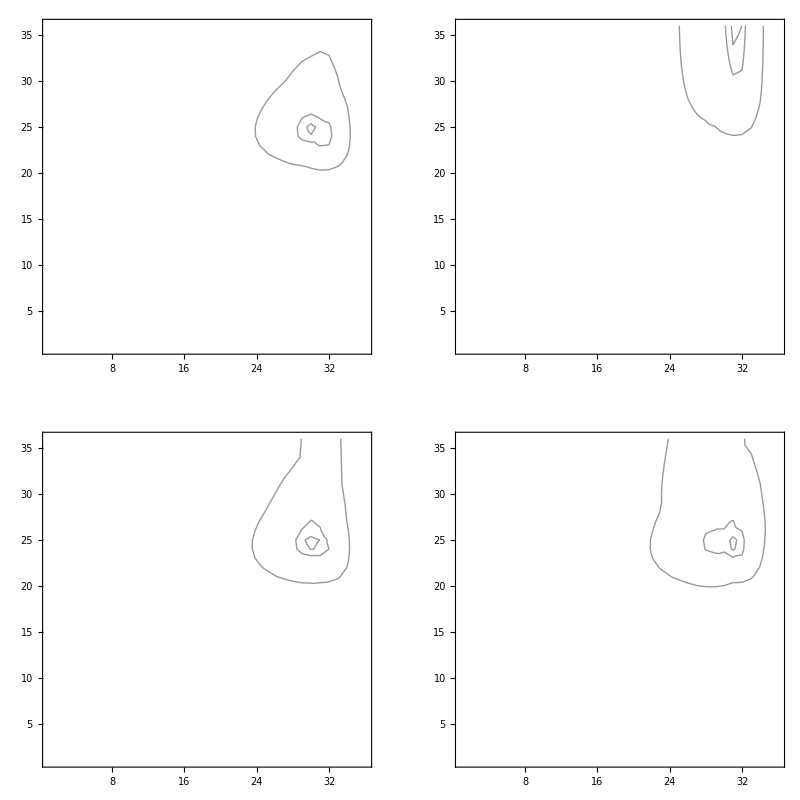

```mathematica
Show[GraphicsArray[{
{ListContourPlot[nd[[1,1]]-Max[nd[[1,1]]],ContourShading->False,Contours->{-2,-10,-100,-1000},PlotRange->{0,-1000}],
ListContourPlot[nd[[1,2]]-Max[nd[[1,2]]],ContourShading->False,Contours->{-2,-10,-100,-1000},PlotRange->{0,-1000}]},
{ListContourPlot[nd[[2,1]]-Max[nd[[2,1]]],ContourShading->False,Contours->{-2,-10,-100,-1000},PlotRange->{0,-1000}],
ListContourPlot[nd[[2,2]]-Max[nd[[2,2]]],ContourShading->False,Contours->{-2,-10,-100,-1000},PlotRange->{0,-1000}]}}]]
```